# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Append[makeColors[7],Gray]
```

{RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.25671741333333337, 0.4331506133333333, 0.8083124666666667],RGBColor[0.36232965333333333, 0.6569880666666666, 0.6428821066666668],RGBColor[0.5586493200000001, 0.73654304, 0.40127688],RGBColor[0.7885816, 0.7225868666666666, 0.26338486666666666],RGBColor[0.90172508, 0.5329993599999999, 0.20705784],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","BQ.1","XBB","XBB.1.5","other"},LabelStyle->{FontSize->11}, LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,0.75}]
```

```mathematica
legendPanelRow=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","BQ.1","XBB","XBB.1.5","other"},LabelStyle->{FontSize->11}, LegendMarkerSize->11,LegendLayout->{"Row",1},Spacings->{0.75,0.75}]
```

```mathematica
colorRamp[t_]:=Blend[{GrayLevel[0.99],Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},(-t+3.5)/2.5]
```

```mathematica
colorRamp[0.5]
```

RGBColor[0.05, 0.05, 0.05]

```mathematica
colorRamp[1.5]
```

RGBColor[0.19963293199999999, 0.3790811759999999, 0.503999862]

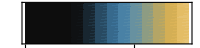

```mathematica
gaPanel=Rotate[DensityPlot[x,{x,0,3},{y,0,1},ColorFunction->colorRamp,ColorFunctionScaling->False,AspectRatio->0.1,PlotRangePadding->0,FrameTicks->{{None,None},{Automatic,None}}, ImageSize->200],Pi/2]
```

## Immune escape

```mathematica
escape=Import["../predictors/predictors.tsv","Table","FieldSeparators"->"\t","Numeric"->False];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding,rbd_count,non_rbd_spike_count,non_spike_count}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6,rbd_count→7,non_rbd_spike_count→8,non_spike_count→9}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
escape=Map[Join[#[[1;;4]],{Interpreter["Number"][#[[5]]],Interpreter["Number"][#[[6]]],Interpreter["Number"][#[[7]]],Interpreter["Number"][#[[8]]],Interpreter["Number"][#[[9]]]}]&,escape];
```

```mathematica
Length[escape]
```

1246

```mathematica
TableForm[RandomSample[escape,10],TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding | rbd_count | non_rbd_spike_count | non_spike_count
BQ.1.1.37 | 22E | BQ.1.1.37 | BA.5.3.1.1.1.1.1.1.37 | 0.831378 | 0.77543 | 6 | 2 | 9
DN.1.1 | 22E | DN.1.1 | BA.5.3.1.1.1.1.1.1.5.1.1 | 0.831378 | 0.77543 | 6 | 3 | 12
XBB.1.38 | 22F | XBB.1.38 | XBB.1.38 | 0.907001 | 0.40687 | 9 | 7 | 6
BA.5.1.11 | 22B | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831 | 3 | 2 | 5
XBB.1.3 | 22F | XBB.1.3 | XBB.1.3 | 0.983269 | 0.49564 | 10 | 6 | 5
DD.1 | 21L | DD.1 | BA.2.3.21.1 | 0.348806 | 0.96834 | 6 | 6 | 3
CH.3.1 | 22D | CH.3.1 | BA.2.75.3.4.1.1.3.1 | 0.670085 | 1.022 | 7 | 5 | 9
BA.2.23.1 | 21L | BA.2.23.1 | BA.2.23.1 | -0.00009 | 0. | 0 | 0 | 5
BA.5.2.63 | 22B | BA.5.2.63 | BA.5.2.63 | 0.630694 | 0.60741 | 5 | 3 | 7
BQ.1.5 | 22E | BQ.1.5 | BA.5.3.1.1.1.1.1.5 | 0.630694 | 0.66401 | 5 | 2 | 9

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
pangoRBDMapping=Map[#[[1]]->#[[7]]&,escape];
```

```mathematica
pangoSpikeMapping=Map[#[[1]]->#[[8]]&,escape];
```

```mathematica
pangoNonSpikeMapping=Map[#[[1]]->#[[9]]&,escape];
```

```mathematica
colorMapping={"21L"->colors[[1]],"22A"->colors[[2]],"22B"->colors[[3]],"22D"->colors[[4]],"22E"->colors[[5]],"22F"->colors[[6]],"23A"->colors[[7]],_->colors[[8]] }
```

{21L→RGBColor[0.30382016, 0.13051672, 0.67703096],22A→RGBColor[0.25671741333333337, 0.4331506133333333, 0.8083124666666667],22B→RGBColor[0.36232965333333333, 0.6569880666666666, 0.6428821066666668],22D→RGBColor[0.5586493200000001, 0.73654304, 0.40127688],22E→RGBColor[0.7885816, 0.7225868666666666, 0.26338486666666666],22F→RGBColor[0.90172508, 0.5329993599999999, 0.20705784],23A→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
Length[ga]
```

356

```mathematica
TableForm[RandomSample[ga,10],TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | BA.2.65 | 1.084 | 1.09 | 1.077
USA | BF.31 | 2.242 | 2.273 | 2.214
USA | BA.2.18 | 1.238 | 1.243 | 1.233
USA | BA.1.1.14 | 0.675 | 0.691 | 0.659
USA | BA.5.6 | 1.806 | 1.809 | 1.803
USA | BN.1.2 | 2.646 | 2.666 | 2.629
USA | BE.1.1.1 | 2.165 | 2.176 | 2.156
USA | BA.5.6.2 | 1.981 | 1.99 | 1.972
USA | BQ.1.1.10 | 2.909 | 2.931 | 2.886
USA | BF.14 | 2.247 | 2.259 | 2.236

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]];
```

```mathematica
Complement[pangoGAMapping[[All,1]],pangoEscapeMapping[[All,1]]]
```

{B.1,B.1.1.529,BA.1,BA.1.1,BA.1.1.1,BA.1.1.10,BA.1.1.14,BA.1.1.16,BA.1.1.18,BA.1.1.2,BA.1.15,BA.1.15.2,BA.1.17.2,BA.1.18,BA.1.20,other}

```mathematica
Length[pangoLineages]
```

340

### Escape

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.003]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.939029

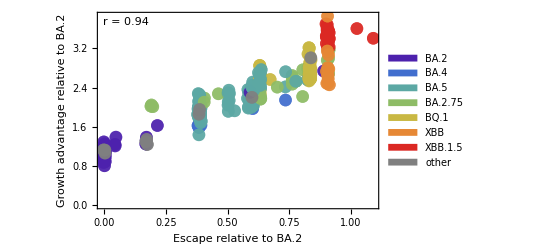

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape relative to BA.2","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

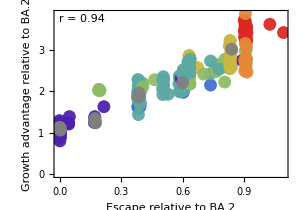

```mathematica
figEscape=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape relative to BA.2","Growth advantage relative to BA.2"},ImageSize->300,AspectRatio->0.7,Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]}]
```

### Binding

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.003]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.756179

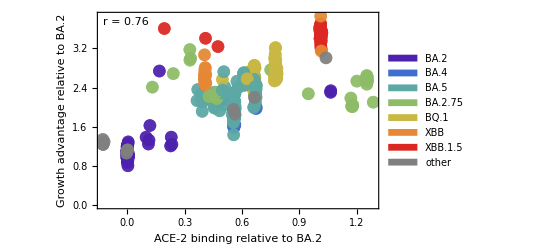

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding relative to BA.2","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

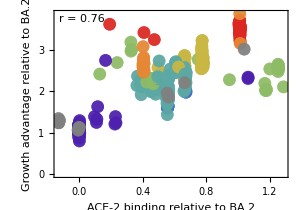

```mathematica
figBinding=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding relative to BA.2","Growth advantage relative to BA.2"},ImageSize->300,AspectRatio->0.7,Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]}]
```

### RBD mutations

```mathematica
rbdGAPairs=Table[{(pangoLineage/.pangoRBDMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
rbdGACorr=Correlation[rbdGAPairs[[All,1]],rbdGAPairs[[All,2]]]
```

0.935469

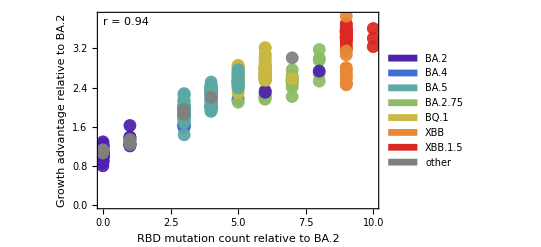

```mathematica
fig=ListPlot[Map[{#}&,rbdGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"RBD mutation count relative to BA.2","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[rbdGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/rbd_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/rbd_growth_advantage_correlation.png

### Non-RBD spike mutations

```mathematica
spikeGAPairs=Table[{(pangoLineage/.pangoSpikeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
spikeGACorr=Correlation[spikeGAPairs[[All,1]],spikeGAPairs[[All,2]]]
```

0.74581

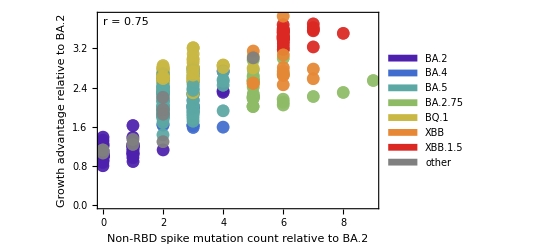

```mathematica
fig=ListPlot[Map[{#}&,spikeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Non-RBD spike mutation count relative to BA.2","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[spikeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/spike_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/spike_growth_advantage_correlation.png

### Non-spike mutations

```mathematica
nonSpikeGAPairs=Table[{(pangoLineage/.pangoNonSpikeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
nonSpikeGACorr=Correlation[nonSpikeGAPairs[[All,1]],nonSpikeGAPairs[[All,2]]]
```

0.604762

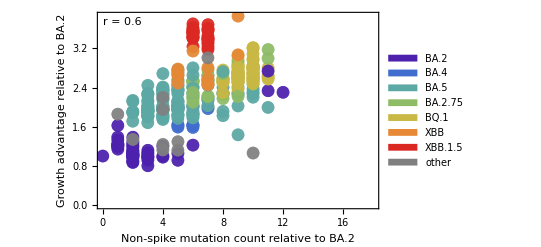

```mathematica
fig=ListPlot[Map[{#}&,nonSpikeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Non-spike mutation count relative to BA.2","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[nonSpikeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/non_spike_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/non_spike_growth_advantage_correlation.png

## Escape / binding / fitness

```mathematica
bindingEscapePairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]]},{pangoLineage,pangoLineages}];
```

```mathematica
bindingEscapeCorr=Correlation[bindingEscapePairs[[All,1]],bindingEscapePairs[[All,2]]]
```

0.711519

```mathematica
bindingEscapeColors=Table[colorRamp[pangoLineage/.pangoGAMapping],{pangoLineage,pangoLineages}];
```

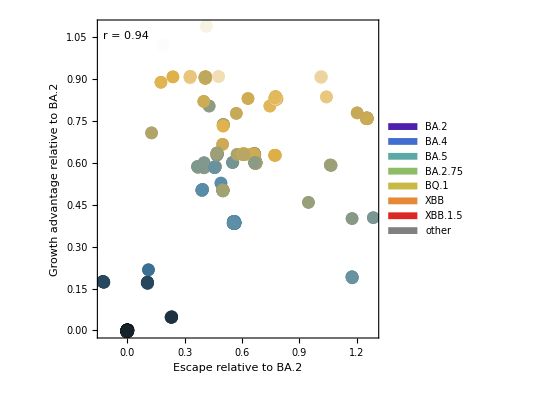

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->bindingEscapeColors,FrameLabel->{"Escape relative to BA.2","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel,AspectRatio->1]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

```mathematica
fig=Grid[{{legendPanelRow,SpanFromLeft},{figBinding,figEscape}},Alignment->Right]
```

| 
-Graphics- | -Graphics-

```mathematica
Export["figures/binding_escape_growth_advantage.png",fig,"PNG",ImageResolution->400]
```

figures/binding_escape_growth_advantage.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1, binding X_2, RBD mutation count X_3, non-RBD spike mutation count X_4 and non-spike mutation count X_5,

### Binding, escape and mutations

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoRBDMapping,pangoLineage/.pangoSpikeMapping,pangoLineage/.pangoNonSpikeMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
regressionData=N[Transpose[Map[Standardize,Transpose[regressionData]]]];
```

```mathematica
lm=LinearModelFit[regressionData,{betaEscape,betaBinding,betaRBD,betaSpike,betaNonSpike},{betaEscape,betaBinding,betaRBD,betaSpike,betaNonSpike}]
```

FittedModel[-1.97555×10^-17+0.157539 betaBinding+0.41273 betaEscape-«21» «12»+0.475608 betaRBD-0.0512191 betaSpike]

```mathematica
lm["RSquared"]
```

0.912367

```mathematica
Sqrt[lm["RSquared"]]
```

0.955179

```mathematica
fig=lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.97555×10^-17 | 0.0161741 | -1.22143×10^-15 | 1
betaEscape | 0.41273 | 0.0685292 | 6.0227 | 4.52407×10^-9
betaBinding | 0.157539 | 0.0239626 | 6.57439 | 1.88175×10^-10
betaRBD | 0.475608 | 0.0846216 | 5.62041 | 4.02296×10^-8
betaSpike | -0.0512191 | 0.0382718 | -1.3383 | 0.181709
betaNonSpike | -0.00187949 | 0.0225321 | -0.083414 | 0.933572

```mathematica
Export["figures/regression_table_with_mutations.png",fig,"PNG",ImageResolution->300]
```

figures/regression_table_with_mutations.png

### Only escape and binding

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
regressionData=N[Transpose[Map[Standardize,Transpose[regressionData]]]];
```

```mathematica
lm=LinearModelFit[regressionData,{betaEscape,betaBinding},{betaEscape,betaBinding}]
```

FittedModel[1.09925×10^-15+0.178987 betaBinding+0.811856 betaEscape]

```mathematica
lm["RSquared"]
```

0.897859

```mathematica
Sqrt[lm["RSquared"]]
```

0.947554

```mathematica
fig=lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.09925×10^-15 | 0.0173839 | 6.32338×10^-14 | 1
betaEscape | 0.811856 | 0.0247676 | 32.779 | 7.63781×10^-107
betaBinding | 0.178987 | 0.0247676 | 7.22666 | 3.33383×10^-12

```mathematica
Export["figures/regression_table_binding_escape.png",fig,"PNG",ImageResolution->300]
```

figures/regression_table_binding_escape.png

### Mutations only

```mathematica
regressionData=Table[{pangoLineage/.pangoRBDMapping,pangoLineage/.pangoSpikeMapping,pangoLineage/.pangoNonSpikeMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
regressionData=N[Transpose[Map[Standardize,Transpose[regressionData]]]];
```

```mathematica
lm=LinearModelFit[regressionData,{betaRBD,betaSpike,betaNonSpike},{betaRBD,betaSpike,betaNonSpike}]
```

FittedModel[-1.11261×10^-15+0.0756924 betaNonSpike+1.01112 betaRBD-0.139726 betaSpike]

```mathematica
lm["RSquared"]
```

0.88743

```mathematica
Sqrt[lm["RSquared"]]
```

0.942035

```mathematica
fig=lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.11261×10^-15 | 0.0182769 | -6.08751×10^-14 | 1
betaRBD | 1.01112 | 0.042319 | 23.8927 | 1.97832×10^-74
betaSpike | -0.139726 | 0.0369541 | -3.78108 | 0.000184763
betaNonSpike | 0.0756924 | 0.0236688 | 3.19799 | 0.00151554

```mathematica
Export["figures/regression_table_mutations_only.png",fig,"PNG",ImageResolution->300]
```

figures/regression_table_mutations_only.png